# Simple binary Turing machines, their numbering, behaviour and output.

## 1. Wolfram’s numbering scheme of Turing machines with s states and k characters, half infinite tape and no explicit halting state.

Number of Turing machines with s states and k characters (binary machines are enligthed) :

```mathematica
Grid[MapThread[Prepend,{Prepend[Table[(2s k)^(s k),{s,2,5},{k,2,5}],{"s"->2,"s"->3,"s"->4,"s"->5}],{"","k"->2,"k"->3,"k"->4,"k"->5}}],Frame->All,Background->{None,{None,Yellow}}]
```

| s→2 | s→3 | s→4 | s→5
k→2 | 4096 | 2985984 | 4294967296 | 10240000000000
k→3 | 2985984 | 198359290368 | 36520347436056576 | 14348907000000000000000
k→4 | 4294967296 | 36520347436056576 | 1208925819614629174706176 | 109951162777600000000000000000000
k→5 | 10240000000000 | 14348907000000000000000 | 109951162777600000000000000000000 | 2980232238769531250000000000000000000000000

Instructions table of a machine whose rule number is given (Wolfram’s conventions as in NKS) :

```mathematica
instructions[tmnumber_,{s_,k_}]:=Flatten[MapIndexed[{1,-1} #2+{0,k}->{1,1,2} Mod[Quotient[#1,{2 k,2,1}],{s,k,2}]+{1,0,-1}&,Partition[IntegerDigits[tmnumber,2 s k,s k],k],{2}]]
```

Shifted instructions are equivalent (number states lowered by 1 and move instructions -1/+1 changed in 0/1) :

```mathematica
shiftedinstructions[tmnumber_,{s_,k_}]:=Flatten[MapIndexed[{1,-1} #2+{-1,k}->{1,1,1} Mod[Quotient[#1,{2 k,2,1}],{s,k,2}]+{0,0,0}&,Partition[IntegerDigits[tmnumber,2 s k,s k],k],{2}]]
```

```mathematica
instructions[2000,{3,2}]
```

{{1,1}→{1,0,-1},{1,0}→{1,0,-1},{2,1}→{1,0,1},{2,0}→{1,0,1},{3,1}→{3,1,-1},{3,0}→{3,0,-1}}

```mathematica
shiftedinstructions[2000,{3,2}]
```

{{0,1}→{0,0,0},{0,0}→{0,0,0},{1,1}→{0,0,1},{1,0}→{0,0,1},{2,1}→{2,1,0},{2,0}→{2,0,0}}

Rule number of a machine whose instructions table is given (Wolfram conventions) :

```mathematica
TMNumber[instructions_,{s_,k_}]:=FromDigits[(#[[2,3]]/.-1->0)+2(#[[2,2]])+2k(#[[2,1]]-1)&/@instructions,2s k]
```

```mathematica
TMNumber[{{1,3}->{1,0,-1},{1,2}->{1,0,-1},{1,1}->{1,0,-1},{1,0}->{1,0,-1},{2,3}->{1,0,-1},{2,2}->{1,0,-1},{2,1}->{1,1,-1},{2,0}->{3,2,-1},{3,3}->{1,1,-1},{3,2}->{2,2,1},{3,1}->{3,3,-1},{3,0}->{2,0,-1}},{3,4}]
```

22596440

Clearly TMNumber annihilates instructions :

```mathematica
TMNumber[instructions[22596440,{3,4}],{3,4}]
```

22596440

The s×k triplets, (s,k,d), associated to a given rule, in Wolfram’s canonical order (s = 1, 2, ...; k = 0, 1, ...; d = -1,+1) :

```mathematica
Triplets[tmnumber_,{s_,k_}]:=instructions[tmnumber,{s,k}][[All,2]]
```

```mathematica
Triplets[22596440,{3,4}]
```

{{1,0,-1},{1,0,-1},{1,0,-1},{1,0,-1},{1,0,-1},{1,0,-1},{1,1,-1},{3,2,-1},{1,1,-1},{2,2,1},{3,3,-1},{2,0,-1}}

The same triplets in shifted mode (s = 0, 1, ...; k = 0, 1, ...; d = 0,1) :

```mathematica
ShiftedTriplets[tmnumber_,{s_,k_}]:=Transpose[MapAt[(#+1)/2&,MapAt[#-1&,Transpose[Triplets[tmnumber,{s,k}]],1],3]]
```

```mathematica
ShiftedTriplets[22596440,{3,4}]
```

{{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,1,0},{2,2,0},{0,1,0},{1,2,1},{2,3,0},{1,0,0}}

Recovering the machine number from the shifted triplets :

```mathematica
TMNumberfromShiftedTriplets[ShiftedTriplets_,{s_,k_}]:=FromDigits[#[[3]]+2#[[2]]+2k#[[1]]&/@ShiftedTriplets,2s k]
```

```mathematica
TMNumberfromShiftedTriplets[{{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,1,0},{2,2,0},{0,1,0},{1,2,1},{2,3,0},{1,0,0}},{3,4}]
```

22596440

```mathematica
An example: MT 2867 (s=2, k=2)
```

An example: MT 2867 (s=2, k=2)

```mathematica
nb=2867;s=2;k=2;limit=8;{Clear[tm];tm=TuringMachine[{nb,s,k},{{1,0},{{},0}},limit];
step=If[MemberQ[Transpose[Transpose[tm][[1]]][[3]],1],First[Position[Transpose[Transpose[tm][[1]]][[3]],1]][[1]],limit]-1;Clear[tm];tm=TuringMachine[{nb,s,k},{{1,0},{{},0}},step];
delta=If[1-Min[Transpose[Transpose[tm][[1]]][[3]]]>0,1-Min[Transpose[Transpose[tm][[1]]][[3]]],0];
tm12=Transpose[Transpose[tm][[1]]][[2]];tm11=Transpose[Transpose[tm][[1]]][[1]];f[nb]=ArrayPlot[Last/@tm,Mesh->True,PlotLabel->{s,k,nb},LabelStyle->Directive[Bold],Epilog->{{Red,Thick,Line[{{delta,0},{delta,step+1}}]},Orange,Thickness[0.15/(step+1)],Arrowheads[0.5/(step+1)],Table[Rotate[Arrow[{{-1/2+tm12[[i]],2/10+1+step-i},{-1/2+tm12[[i]],4/5+1+step-i}}],-2π/s(tm11[[i]]-1)],{i,step+1}]}]};f[nb]
```

-Graphics-

```mathematica
shiftedinstructions[2867,{2,2}]
```

{{0,1}→{1,0,1},{0,0}→{1,0,0},{1,1}→{1,1,0},{1,0}→{0,1,1}}

```mathematica
ShiftedTriplets[2867,{2,2}]
```

{{1,0,1},{1,0,0},{1,1,0},{0,1,1}}

```mathematica
a[_]=0;sigma=0;n=0;
```

```mathematica
7-2sigma-a[n]
```

7

## Analysis of the 4096 2-states binary machines.

## Activation of preliminary instructions :

```mathematica
SingleTMStep[rule_, {s_, tape_, pos_} /; pos<1] := {s, tape, pos}
```

```mathematica
SingleTMStep[rule_, {s_, tape_, pos_} /; pos>Length[tape]] := SingleTMStep[rule,{s, Prepend[tape,0], pos}]
```

```mathematica
SingleTMStep[rule_, {s_, tape_, pos_}] := Apply[{#1,ReplacePart[tape,#2,-pos],pos-#3}&,Replace[{s,tape[[-pos]]},rule]]
```

```mathematica
SingleTMEvolve[rule_, tape_, bound_] := NestWhile[SingleTMStep[rule, #]&, {1,tape,1}, ( 5>#[[3]]>0)&,1,bound]  (*  !!!!!!!!!  *)
```

```mathematica
SingleTMEvolveList[rule_, tape_, bound_] := NestWhileList[SingleTMStep[rule, #]&, {1,tape,1},( 5>#[[3]]>0)&,1,bound]   (*  !!!!!!!!!  *)
```

```mathematica
SingleTMEvolveList[instructions[2867,{2,2}],{0}, 8]    (*Displays : {state, {list from most left read cell to red line}, head position counted from the red line, 0 = Halt}*)
```

{{1,{0},1},{2,{0},2},{1,{1,0},1},{2,{1,0},2},{2,{1,0},3},{1,{1,1,0},2},{2,{1,0,0},1},{1,{1,0,1},0}}

```mathematica
conjugate[li_]:=li/.{0->u,1->v}/.{u->1,v->0}
```

## Search for the first time a new sequence is printed :

```mathematica
Timing[result={{0},{1}};index={64,64};depth={1,1};Do[{
twostatesset=Sort[Flatten[Table[TMNumberfromShiftedTriplets[{{s1,k1,d1},{s2,k2,0},{s3,k3,d3},{s4,k4,d4}},{2,2}],{s3,0,1},{k3,0,1},{d3,0,1},{s4,0,1},{k4,0,1},{d4,0,1}]]];
twostatessubset1=Sort[DeleteDuplicates[Flatten[Table[TMNumberfromShiftedTriplets[{{s1,k1,d1},{s2,k2,0},{s3,k3,d3},{s4,k4,0}},{2,2}],{s3,0,1},{k3,0,1},{d3,0,1},{s4,0,1},{k4,0,1},{d4,0,1}]]]];
twostatessubset2=Sort[DeleteDuplicates[Flatten[Table[TMNumberfromShiftedTriplets[{{s1,k1,d1},{1,0,0},{s3,k3,d3},{0,0,1}},{2,2}],{s3,0,1},{k3,0,1},{d3,0,1},{s4,0,1},{k4,0,1},{d4,0,1}]]]];
twostatessubset3=Sort[DeleteDuplicates[Flatten[Table[If[s4==0 ∧ k2==0,{},TMNumberfromShiftedTriplets[{{s1,k1,If[2s4+2-k2==1,1,d1]},{1,k2,0},{s3,k3,If[2s4+2-k2==3,1,d3]},{s4,k4,1}},{2,2}]],{s3,0,1},{k3,0,1},{d3,0,1},{s4,0,1},{k4,0,1},{d4,0,1}]]]];

twostatesreducedset=Complement[twostatesset,Union[twostatessubset1,twostatessubset2,twostatessubset2]],
Do[
{z=SingleTMEvolveList[instructions[twostatesreducedset[[j]],{2,2}],{0},8], If[Last[z][[3]]==0,{If[FreeQ[result,Last[z][[2]]],{index=Append[index,twostatesreducedset[[j]]],depth=Append[depth,Length[z]/2]}];result=DeleteDuplicates[Join[Append[result,Last[z][[2]]]]],If[FreeQ[result,Reverse[Last[z][[2]]]],{index=Append[index,twostatesreducedset[[j]]],depth=Append[depth,Length[z]/2]}],result=DeleteDuplicates[Join[Append[result,Reverse[Last[z][[2]]]]]],If[FreeQ[result,conjugate[Last[z][[2]]]],{index=Append[index,twostatesreducedset[[j]]],depth=Append[depth,Length[z]/2]}],result=DeleteDuplicates[Join[Append[result,conjugate[Last[z][[2]]]]]],If[FreeQ[result,conjugate[Reverse[Last[z][[2]]]]],{index=Append[index,twostatesreducedset[[j]]],depth=Append[depth,Length[z]/2]}],result=DeleteDuplicates[Join[Append[result,conjugate[Reverse[Last[z][[2]]]]]]]}]},      {j,Length[twostatesreducedset]}]},
{s1,0,1},{k1,0,1},{d1,0,1},{s2,1,1},{k2,0,1}]]
```

{0.109,Null}

```mathematica
result
```

{{0},{1},{0,0},{1,1},{0,1},{1,0},{1,1,1},{0,0,0},{1,0,1},{0,1,0}}

```mathematica
index
```

{64,64,261,261,299,299,423,423,2867,2867}

```mathematica
depth
```

{1,1,2,2,3,3,4,4,4,4}

## Summary when s=2 (Symmetric sequences have been set as equals) :

```mathematica
Labeled[Grid[Prepend[Flatten[Partition[Transpose[{Table[k,{k,2,1+Length[index]}],result,Table[Rest[IntegerDigits[k,2]]->IntegerLength[k,2]-1,{k,2,1+Length[index]}],depth,index}],Length[index]],1],{"Serial number","Sequence","Complexity","Logical Depth","TM Number"}],Frame->All,Background->LightPink],"s=2"]
```

Serial number | Sequence | Complexity | Logical Depth | TM Number
2 | {0} | {0}→1 | 1 | 64
3 | {1} | {1}→1 | 1 | 64
4 | {0,0} | {0,0}→2 | 2 | 261
5 | {1,1} | {0,1}→2 | 2 | 261
6 | {0,1} | {1,0}→2 | 3 | 299
7 | {1,0} | {1,1}→2 | 3 | 299
8 | {1,1,1} | {0,0,0}→3 | 4 | 423
9 | {0,0,0} | {0,0,1}→3 | 4 | 423
10 | {1,0,1} | {0,1,0}→3 | 4 | 2867
11 | {0,1,0} | {0,1,1}→3 | 4 | 2867s=2

## Analysis of the 2985984 3-states binary machines.

## Activation of preliminary instructions :

```mathematica
SingleTMStep[rule_, {s_, tape_, pos_} /; pos<1] := {s, tape, pos}
```

```mathematica
SingleTMStep[rule_, {s_, tape_, pos_} /; pos>Length[tape]] := SingleTMStep[rule,{s, Prepend[tape,0], pos}]
```

```mathematica
SingleTMStep[rule_, {s_, tape_, pos_}] := Apply[{#1,ReplacePart[tape,#2,-pos],pos-#3}&,Replace[{s,tape[[-pos]]},rule]]
```

```mathematica
SingleTMEvolve[rule_, tape_, bound_] := NestWhile[SingleTMStep[rule, #]&, {1,tape,1}, ( 8>#[[3]]>0)&,1,bound]  (*  !!!!!!!!!  *)
```

```mathematica
SingleTMEvolveList[rule_, tape_, bound_] := NestWhileList[SingleTMStep[rule, #]&, {1,tape,1},( 8>#[[3]]>0)&,1,bound]   (*  !!!!!!!!!  *)
```

```mathematica
conjugate[li_]:=li/.{0->u,1->v}/.{u->1,v->0}
```

## Search for new sequences :

```mathematica
Timing[result={{0},{1},{0,0},{1,1},{0,1},{1,0},{1,1,1},{0,0,0},{1,0,1},{0,1,0}};index={64,64,261,261,299,299,423,423,2867,2867};depth={1,1,3,3,5,5,7,7,7,7};Do[{
threestatesset=Sort[Flatten[Table[TMNumberfromShiftedTriplets[{{s1,k1,d1},{s2,k2,d2},{s3,k3,d3},{s4,k4,d4},{s5,k5,d5},{s6,k6,d6}},{3,2}],{s2,0,2},{s3,0,2},{s4,0,2},{s5,0,2},{s6,0,2},{k2,0,1},{k3,0,1},{k4,0,1},{k5,0,1},{k6,0,1},{d2,0,1},{d3,0,1},{d4,0,1},{d5,0,1},{d6,0,1}]]];
threestatessubset1=Sort[Flatten[Table[TMNumberfromShiftedTriplets[{{s1,k1,d1},{s2,k2,0},{s3,k3,d3},{s4,k4,0},{s5,k5,d5},{s6,k6,0}},{3,2}],{s2,0,2},{s3,0,2},{s4,0,2},{s5,0,2},{s6,0,2},{k2,0,1},{k3,0,1},{k4,0,1},{k5,0,1},{k6,0,1},{d3,0,1},{d5,0,1}]]];
threestatessubset2=Sort[Flatten[Table[TMNumberfromShiftedTriplets[{{s1,k1,d1},{0,k2,0},{s3,k3,d3},{s4,k4,d4},{s5,k5,d5},{s6,k6,d6}},{3,2}],{s3,0,2},{s4,0,2},{s5,0,2},{s6,0,2},{k2,0,1},{k3,0,1},{k4,0,1},{k5,0,1},{k6,0,1},{d3,0,1},{d4,0,1},{d5,0,1},{d6,0,1}]]];
threestatessubset3=Sort[Flatten[Union[    
Table[TMNumberfromShiftedTriplets[{{s1,k1,d1},{1,k2,0},{s3,k3,d3},{s4,k4,0},{s5,k5,d5},{s6,k6,d6}},{3,2}],{s3,0,2},{s4,0,1},{s5,0,2},{s6,0,2},{k2,0,1},{k3,0,1},{k4,0,1},{k5,0,1},{k6,0,1},{d3,0,1},{d5,0,1},{d6,0,1}], 

Table[TMNumberfromShiftedTriplets[{{s1,k1,d1},{2,k2,0},{s3,k3,d3},{s4,k4,d4},{s5,k5,d5},{s6,k6,0}},{3,2}],{s3,0,2},{s4,0,2},{s5,0,2},{s6,0,2,2},{k2,0,1},{k3,0,1},{k4,0,1},{k5,0,1},{k6,0,1},{d3,0,1},{d4,0,1},{d5,0,1}]  ]]];
threestatessubset4=Sort[Flatten[Union[
Table[TMNumberfromShiftedTriplets[{{s1,k1,d1},{1,0,0},{s3,k3,d3},{0,0,1},{s5,k5,d5},{s6,k6,d6}},{3,2}],{s3,0,2},{s5,0,2},{s6,0,2},{k3,0,1},{k5,0,1},{k6,0,1},{d3,0,1},{d5,0,1},{d6,0,1}],

 Table[TMNumberfromShiftedTriplets[{{s1,k1,d1},{2,0,0},{s3,k3,d3},{s4,k4,d4},{s5,k5,d5},{0,0,1}},{3,2}],{s3,0,2},{s5,0,2},{s6,0,2},{k3,0,1},{k4,0,1},{k5,0,1},{d3,0,1},{d4,0,1},{d5,0,1}] ]]];
threestatessubset5=Sort[Flatten[Table[TMNumberfromShiftedTriplets[{{s1,k1,d1},{s2,0,1},{s3,k3,d3},{s4,k4,d4},{s5,k5,d5},{s6,k6,d6}},{3,2}],{s2,0,2},{s3,0,2},{s4,0,2},{s5,0,2},{s6,0,2},{k3,0,1},{k4,0,1},{k5,0,1},{k6,0,1},{d3,0,1},{d4,0,1},{d5,0,1},{d6,0,1}]]];
threestatessubset6=Sort[Flatten[Table[TMNumberfromShiftedTriplets[{{s1,k1,d1},{s2,1,1},{s3,k3,d3},{s4,k4,d4},{s5,k5,d5},{s6,k6,d6}},{3,2}],{s2,0,2},{s3,0,2},{s4,0,2},{s5,0,2},{s6,0,2},{k3,0,1},{k4,0,1},{k5,0,1},{k6,0,1},{d3,0,1},{d4,0,1},{d5,0,1},{d6,0,1}]]];
threestatessubset7=Sort[DeleteDuplicates[Flatten[Table[If[s4==0 ∧ k2==0,{},TMNumberfromShiftedTriplets[{{s1,k1,If[2s4+2-k2==1,1,d1]},{1,k2,0},{s3,k3,If[2s4+2-k2==3,1,d3]},{s4,k4,1},{s5,k5,If[2s4+2-k2==5,1,d5]},{s6,k6,If[2s4+2-k2==6,1,d6]}},{3,2}]],{s4,0,2},{k2,0,1},{s3,0,2},{s5,0,2},{s6,0,2},{k3,0,1},{k4,0,1},{k5,0,1},{k6,0,1},{d3,0,1},{d5,0,1},{d6,0,1}]]]];
threestatessubset8=Sort[DeleteDuplicates[Flatten[Table[If[s6==0 ∧ k2==0,{},TMNumberfromShiftedTriplets[{{s1,k1,If[2s6+2-k2==1,1,d1]},{2,k2,0},{s3,k3,If[2s6+2-k2==3,1,d3]},{s4,k4,If[2s6+2-k2==4,1,d4]},{s5,k5,If[2s6+2-k2==5,1,d5]},{s6,k6,1}},{3,2}]],{s6,0,2},{k2,0,1},{s3,0,2},{s4,0,2},{s5,0,2},{k3,0,1},{k4,0,1},{k5,0,1},{k6,0,1},{d3,0,1},{d4,0,1},{d5,0,1}]]]];
threestatesreducedset=Complement[threestatesset,Union[threestatessubset1,threestatessubset2,threestatessubset3,threestatessubset4,threestatessubset5,threestatessubset6,threestatessubset7,threestatessubset8]],
Do[
{z=SingleTMEvolveList[instructions[threestatesreducedset[[j]],{3,2}],{0},22], If[Last[z][[3]]==0,{If[FreeQ[result,Last[z][[2]]],{index=Append[index,threestatesreducedset[[j]]],depth=Append[depth,Length[z]/2]}];result=DeleteDuplicates[Join[Append[result,Last[z][[2]]]]],If[FreeQ[result,Reverse[Last[z][[2]]]],{index=Append[index,threestatesreducedset[[j]]],depth=Append[depth,Length[z]/2]}],result=DeleteDuplicates[Join[Append[result,Reverse[Last[z][[2]]]]]],If[FreeQ[result,conjugate[Last[z][[2]]]],{index=Append[index,threestatesreducedset[[j]]],depth=Append[depth,Length[z]/2]}],result=DeleteDuplicates[Join[Append[result,conjugate[Last[z][[2]]]]]],If[FreeQ[result,conjugate[Reverse[Last[z][[2]]]]],{index=Append[index,threestatesreducedset[[j]]],depth=Append[depth,Length[z]/2]}],result=DeleteDuplicates[Join[Append[result,conjugate[Reverse[Last[z][[2]]]]]]]}]},      {j,Length[threestatesreducedset]}]},
{s1,0,2},{k1,0,1},{d1,0,1}]]
```

$Aborted

```mathematica
result
```

{{0},{1},{0,0},{1,1},{0,1},{1,0},{1,1,1},{0,0,0},{1,0,1},{0,1,0},{0,0,1},{1,0,0},{1,1,0},{0,1,1},{1,1,1,1},{0,0,0,0},{0,1,1,1},{1,1,1,0},{1,0,0,0},{0,0,0,1},{1,0,1,0},{0,1,0,1},{1,1,0,0},{0,0,1,1},{1,1,0,1},{1,0,1,1},{0,0,1,0},{0,1,0,0},{1,1,1,1,1},{0,0,0,0,0},{1,0,1,0,1},{0,1,0,1,0},{1,1,1,1,1,1},{0,0,0,0,0,0},{1,0,0,1},{0,1,1,0},{1,1,1,1,0},{0,1,1,1,1},{0,0,0,0,1},{1,0,0,0,0},{1,0,1,1,1,1},{1,1,1,1,0,1},{0,1,0,0,0,0},{0,0,0,0,1,0},{1,1,0,0,1},{1,0,0,1,1},{0,0,1,1,0},{0,1,1,0,0},{1,0,0,0,1},{0,1,1,1,0}}

```mathematica
index
```

{64,64,261,261,299,299,423,423,2867,2867,84211,84211,84211,84211,84491,84491,96557,96557,96557,96557,98418,98418,98466,98466,99775,99775,99775,99775,125963,125963,141463,141463,1138187,1138187,1339072,1339072,1377015,1377015,1377015,1377015,1423659,1423659,1423659,1423659,1428930,1428930,1428930,1428930,1874607,1874607}

```mathematica
depth
```

{1,1,2,2,3,3,4,4,4,4,5,5,5,5,5,5,6,6,6,6,5,5,6,6,7,7,7,7,9,9,7,7,9,9,8,8,11,11,11,11,10,10,10,10,9,9,9,9,10,10}

```mathematica
Labeled[Grid[Prepend[Flatten[Partition[Transpose[{Table[k,{k,2,1+Length[index]}],result,Table[Rest[IntegerDigits[k,2]]->IntegerLength[k,2]-1,{k,2,1+Length[index]}],depth,index}],Length[index]],1],{"Serial number","Sequence","Complexity","Logical Depth","TM Number"}],Frame->All,Background->{None,Flatten[Join[Table[k->LightRed,{k,11}],Table[k->LightBlue,{k,12,51}]]]}],"s=2,3"]
```

```mathematica
{{"Serial number", "Sequence", "Complexity", "Logical Depth", "TM Number"}, {2, {0}, {0}->1, 1, 64}, {3, {1}, {1}->1, 1, 64}, {4, {0,0}, {0,0}->2, 2, 261}, {5, {1,1}, {0,1}->2, 2, 261}, {6, {0,1}, {1,0}->2, 3, 299}, {7, {1,0}, {1,1}->2, 3, 299}, {8, {1,1,1}, {0,0,0}->3, 4, 423}, {9, {0,0,0}, {0,0,1}->3, 4, 423}, {10, {1,0,1}, {0,1,0}->3, 4, 2867}, {11, {0,1,0}, {0,1,1}->3, 4, 2867}, {12, {0,0,1}, {1,0,0}->3, 5, 84211}, {13, {1,0,0}, {1,0,1}->3, 5, 84211}, {14, {1,1,0}, {1,1,0}->3, 5, 84211}, {15, {0,1,1}, {1,1,1}->3, 5, 84211}, {16, {1,1,1,1}, {0,0,0,0}->4, 5, 84491}, {17, {0,0,0,0}, {0,0,0,1}->4, 5, 84491}, {18, {0,1,1,1}, {0,0,1,0}->4, 6, 96557}, {19, {1,1,1,0}, {0,0,1,1}->4, 6, 96557}, {20, {1,0,0,0}, {0,1,0,0}->4, 6, 96557}, {21, {0,0,0,1}, {0,1,0,1}->4, 6, 96557}, {22, {1,0,1,0}, {0,1,1,0}->4, 5, 98418}, {23, {0,1,0,1}, {0,1,1,1}->4, 5, 98418}, {24, {1,1,0,0}, {1,0,0,0}->4, 6, 98466}, {25, {0,0,1,1}, {1,0,0,1}->4, 6, 98466}, {26, {1,1,0,1}, {1,0,1,0}->4, 7, 99775}, {27, {1,0,1,1}, {1,0,1,1}->4, 7, 99775}, {28, {0,0,1,0}, {1,1,0,0}->4, 7, 99775}, {29, {0,1,0,0}, {1,1,0,1}->4, 7, 99775}, {30, {1,1,1,1,1}, {1,1,1,0}->4, 9, 125963}, {31, {0,0,0,0,0}, {1,1,1,1}->4, 9, 125963}, {32, {1,0,1,0,1}, {0,0,0,0,0}->5, 7, 141463}, {33, {0,1,0,1,0}, {0,0,0,0,1}->5, 7, 141463}, {34, {1,1,1,1,1,1}, {0,0,0,1,0}->5, 9, 1138187}, {35, {0,0,0,0,0,0}, {0,0,0,1,1}->5, 9, 1138187}, {36, {1,0,0,1}, {0,0,1,0,0}->5, 8, 1339072}, {37, {0,1,1,0}, {0,0,1,0,1}->5, 8, 1339072}, {38, {1,1,1,1,0}, {0,0,1,1,0}->5, 11, 1377015}, {39, {0,1,1,1,1}, {0,0,1,1,1}->5, 11, 1377015}, {40, {0,0,0,0,1}, {0,1,0,0,0}->5, 11, 1377015}, {41, {1,0,0,0,0}, {0,1,0,0,1}->5, 11, 1377015}, {42, {1,0,1,1,1,1}, {0,1,0,1,0}->5, 10, 1423659}, {43, {1,1,1,1,0,1}, {0,1,0,1,1}->5, 10, 1423659}, {44, {0,1,0,0,0,0}, {0,1,1,0,0}->5, 10, 1423659}, {45, {0,0,0,0,1,0}, {0,1,1,0,1}->5, 10, 1423659}, {46, {1,1,0,0,1}, {0,1,1,1,0}->5, 9, 1428930}, {47, {1,0,0,1,1}, {0,1,1,1,1}->5, 9, 1428930}, {48, {0,0,1,1,0}, {1,0,0,0,0}->5, 9, 1428930}, {49, {0,1,1,0,0}, {1,0,0,0,1}->5, 9, 1428930}, {50, {1,0,0,0,1}, {1,0,0,1,0}->5, 10, 1874607}, {51, {0,1,1,1,0}, {1,0,0,1,1}->5, 10, 1874607}}"s=2,3"
```

```mathematica
An example :
```

```mathematica
nb=2867;s=2;k=2;limit=22;{Clear[tm];tm=TuringMachine[{nb,s,k},{{1,0},{{},0}},limit];
step=If[MemberQ[Transpose[Transpose[tm][[1]]][[3]],1],First[Position[Transpose[Transpose[tm][[1]]][[3]],1]][[1]],limit]-1;Clear[tm];tm=TuringMachine[{nb,s,k},{{1,0},{{},0}},step];
delta=If[1-Min[Transpose[Transpose[tm][[1]]][[3]]]>0,1-Min[Transpose[Transpose[tm][[1]]][[3]]],0];
tm12=Transpose[Transpose[tm][[1]]][[2]];tm11=Transpose[Transpose[tm][[1]]][[1]];f[nb]=ArrayPlot[Last/@tm,Mesh->True,PlotLabel->{s,k,nb},LabelStyle->Directive[Bold],Epilog->{{Red,Thick,Line[{{delta,0},{delta,step+1}}]},Orange,Thickness[0.15/(step+1)],Arrowheads[0.5/(step+1)],Table[Rotate[Arrow[{{-1/2+tm12[[i]],2/10+1+step-i},{-1/2+tm12[[i]],4/5+1+step-i}}],-2π/s(tm11[[i]]-1)],{i,step+1}]}]};f[nb]
```

-Graphics-

## Analysis of the 4294967296 4-states binary machines (Incomplete).

## Activation of preliminary instructions :

```mathematica
SingleTMStep[rule_, {s_, tape_, pos_} /; pos<1] := {s, tape, pos}
```

```mathematica
SingleTMStep[rule_, {s_, tape_, pos_} /; pos>Length[tape]] := SingleTMStep[rule,{s, Prepend[tape,0], pos}]
```

```mathematica
SingleTMStep[rule_, {s_, tape_, pos_}] := Apply[{#1,ReplacePart[tape,#2,-pos],pos-#3}&,Replace[{s,tape[[-pos]]},rule]]
```

```mathematica
SingleTMEvolve[rule_, tape_, bound_] := NestWhile[SingleTMStep[rule, #]&, {1,tape,1}, ( 18>#[[3]]>0)&,1,bound]  (*  !!!!!!!!!  *)
```

```mathematica
SingleTMEvolveList[rule_, tape_, bound_] := NestWhileList[SingleTMStep[rule, #]&, {1,tape,1},( 18>#[[3]]>0)&,1,bound]   (*  !!!!!!!!!  *)
```

```mathematica
conjugate[li_]:=li/.{0->u,1->v}/.{u->1,v->0}
```

## Search for new sequences :

```mathematica
Timing[result={{0},{1},{0,0},{1,1},{0,1},{1,0},{1,1,1},{0,0,0},{1,0,1},{0,1,0},{0,0,1},{1,0,0},{1,1,0},{0,1,1},{1,1,1,1},{0,0,0,0},{0,1,1,1},{1,1,1,0},{1,0,0,0},{0,0,0,1},{1,0,1,0},{0,1,0,1},{1,1,0,0},{0,0,1,1},{1,1,0,1},{1,0,1,1},{0,0,1,0},{0,1,0,0},{1,1,1,1,1},{0,0,0,0,0},{1,0,1,0,1},{0,1,0,1,0},{1,1,1,1,1,1},{0,0,0,0,0,0},{1,0,0,1},{0,1,1,0},{1,1,1,1,0},{0,1,1,1,1},{0,0,0,0,1},{1,0,0,0,0},{1,0,1,1,1,1},{1,1,1,1,0,1},{0,1,0,0,0,0},{0,0,0,0,1,0},{1,1,0,0,1},{1,0,0,1,1},{0,0,1,1,0},{0,1,1,0,0},{1,0,0,0,1},{0,1,1,1,0}};depth={1,1,3,3,5,5,7,7,7,7,9,9,9,9,9,9,11,11,11,11,9,9,11,11,13,13,13,13,17,17,13,13,17,17,15,15,21,21,21,21,19,19,19,19,17,17,17,17,19,19};index={64,64,261,261,299,299,423,423,2867,2867,84211,84211,84211,84211,84491,84491,96557,96557,96557,96557,98418,98418,98466,98466,99775,99775,99775,99775,125963,125963,141463,141463,1138187,1138187,1339072,1339072,1377015,1377015,1377015,1377015,1423659,1423659,1423659,1423659,1428930,1428930,1428930,1428930,1874607,1874607};Do[{
fourstatesset=Sort[Flatten[Table[TMNumberfromShiftedTriplets[{{s1,k1,d1},{s2,k2,0},{s3,k3,d3},{s4,k4,d4},{s5,k5,d5},{s6,k6,d6},{s7,k7,d7},{s8,k8,d8}},{4,2}],{s4,0,3},{s5,0,3},{s6,0,3},{s7,0,3},{s8,0,3},{k4,0,1},{k5,0,1},{k6,0,1},{k7,0,1},{k8,0,1},{d4,0,1},{d5,0,1},{d6,0,1},{d7,0,1},{d8,0,1}]]];
fourstatessubset1=Sort[DeleteDuplicates[Flatten[Table[TMNumberfromShiftedTriplets[{{s1,k1,d1},{s2,k2,0},{s3,k3,d3},{s4,k4,0},{s5,k5,d5},{s6,k6,0},{s7,k7,d7},{s8,k8,0}},{4,2}],{s4,0,3},{s5,0,3},{s6,0,3},{s7,0,3},{s8,0,3},{k4,0,1},{k5,0,1},{k6,0,1},{k7,0,1},{k8,0,1},{d5,0,1},{d7,0,1}]]]];

fourstatessubset3=Sort[DeleteDuplicates[Flatten[Union[    
Table[TMNumberfromShiftedTriplets[{{s1,k1,d1},{1,k2,0},{s3,k3,d3},{s4,k4,0},{s5,k5,d5},{s6,k6,d6},{s7,k7,d7},{s8,k8,d8}},{4,2}],{s4,0,1},{s5,0,3},{s6,0,3},{s7,0,3},{s8,0,3},{k4,0,1},{k5,0,1},{k6,0,1},{k7,0,1},{k8,0,1},{d5,0,1},{d6,0,1},{d7,0,1},{d8,0,1}], 

Table[TMNumberfromShiftedTriplets[{{s1,k1,d1},{2,k2,0},{s3,k3,d3},{s4,k4,d4},{s5,k5,d5},{s6,k6,0},{s7,k7,d7},{s8,k8,d8}},{4,2}],{s4,0,3},{s5,0,3},{s6,0,2,2},{s7,0,3},{s8,0,3},{k4,0,1},{k5,0,1},{k6,0,1},{k7,0,1},{k8,0,1},{d4,0,1},{d5,0,1},{d7,0,1},{d8,0,1}] ,

Table[TMNumberfromShiftedTriplets[{{s1,k1,d1},{3,k2,0},{s3,k3,d3},{s4,k4,d4},{s5,k5,d5},{s6,k6,d6},{s7,k7,d7},{s8,k8,0}},{4,2}],{s4,0,3},{s5,0,3},{s6,0,3},{s7,0,3},{s8,0,3,3},{k4,0,1},{k5,0,1},{k6,0,1},{k7,0,1},{k8,0,1},{d4,0,1},{d5,0,1},{d6,0,1},{d7,0,1}] ]]]];
fourstatessubset4=Sort[DeleteDuplicates[Flatten[Union[
Table[TMNumberfromShiftedTriplets[{{s1,k1,d1},{1,0,0},{s3,k3,d3},{0,0,1},{s5,k5,d5},{s6,k6,d6},{s7,k7,d7},{s8,k8,d8}},{4,2}],{s5,0,3},{s6,0,3},{s7,0,3},{s8,0,3},{k5,0,1},{k6,0,1},{k7,0,1},{k8,0,1},{d5,0,1},{d6,0,1},{d7,0,1},{d8,0,1}],

 Table[TMNumberfromShiftedTriplets[{{s1,k1,d1},{2,0,0},{s3,k3,d3},{s4,k4,d4},{s5,k5,d5},{0,0,1},{s7,k7,d7},{s8,k8,d8}},{4,2}],{s4,0,3},{s5,0,3},{s7,0,3},{s8,0,3},{k4,0,1},{k5,0,1},{k7,0,1},{k8,0,1},{d4,0,1},{d5,0,1},{d7,0,1},{d8,0,1}] ,

 Table[TMNumberfromShiftedTriplets[{{s1,k1,d1},{3,0,0},{s3,k3,d3},{s4,k4,d4},{s5,k5,d5},{s6,k6,d6},{s7,k7,d7},{0,0,1}},{4,2}],{s4,0,3},{s5,0,3},{s6,0,3},{s7,0,3},{k4,0,1},{k5,0,1},{k6,0,1},{k7,0,1},{d4,0,1},{d5,0,1},{d6,0,1},{d7,0,1}] ]]]];

fourstatessubset7=Sort[DeleteDuplicates[Flatten[Table[If[s4==0 ∧ k2==0,{},TMNumberfromShiftedTriplets[{{s1,k1,If[2s4+2-k2==1,1,d1]},{1,k2,0},{s3,k3,If[2s4+2-k2==3,1,d3]},{s4,k4,1},{s5,k5,If[2s4+2-k2==5,1,d5]},{s6,k6,If[2s4+2-k2==6,1,d6]},{s7,k7,If[2s4+2-k2==7,1,d7]},{s8,k8,If[2s4+2-k2==8,1,d8]}},{4,2}]],{s4,0,3},{s5,0,3},{s6,0,3},{s7,0,3},{s8,0,3},{k4,0,1},{k5,0,1},{k6,0,1},{k7,0,1},{k8,0,1},{d5,0,1},{d6,0,1},{d7,0,1},{d8,0,1}]]]];
fourstatessubset8=Sort[DeleteDuplicates[Flatten[Table[If[s6==0 ∧ k2==0,{},TMNumberfromShiftedTriplets[{{s1,k1,If[2s6+2-k2==1,1,d1]},{2,k2,0},{s3,k3,If[2s6+2-k2==3,1,d3]},{s4,k4,If[2s6+2-k2==4,1,d4]},{s5,k5,If[2s6+2-k2==5,1,d5]},{s6,k6,1},{s7,k7,If[2s6+2-k2==7,1,d7]},{s8,k8,If[2s6+2-k2==8,1,d8]}},{4,2}]],{s4,0,3},{s5,0,3},{s6,0,3},{s7,0,3},{s8,0,3},{k4,0,1},{k5,0,1},{k6,0,1},{k7,0,1},{k8,0,1},{d4,0,1},{d5,0,1},{d7,0,1},{d8,0,1}]]]];

fourstatessubset9=Sort[DeleteDuplicates[Flatten[Table[If[s8==0 ∧ k2==0,{},TMNumberfromShiftedTriplets[{{s1,k1,If[2s8+2-k2==1,1,d1]},{3,k2,0},{s3,k3,If[2s8+2-k2==3,1,d3]},{s4,k4,If[2s8+2-k2==4,1,d4]},{s5,k5,If[2s8+2-k2==5,1,d5]},{s6,k6,If[2s8+2-k2==6,1,d6]},{s7,k7,If[2s8+2-k2==7,1,d7]},{s8,k8,1}},{4,2}]],{s4,0,3},{s5,0,3},{s6,0,3},{s7,0,3},{s8,0,3},{k4,0,1},{k5,0,1},{k6,0,1},{k7,0,1},{k8,0,1},{d4,0,1},{d5,0,1},{d6,0,1},{d7,0,1}]]]];

fourstatesreducedset=Complement[fourstatesset,fourstatessubset1,fourstatessubset3,fourstatessubset4,fourstatessubset7,fourstatessubset8,fourstatessubset9],
Do[
{z=SingleTMEvolveList[instructions[fourstatesreducedset[[j]],{4,2}],{0},110], If[Last[z][[3]]==0,{If[FreeQ[result,Last[z][[2]]],{index=Append[index,fourstatesreducedset[[j]]],depth=Append[depth,Length[z]-1]}];result=DeleteDuplicates[Join[Append[result,Last[z][[2]]]]],If[FreeQ[result,Reverse[Last[z][[2]]]],{index=Append[index,fourstatesreducedset[[j]]],depth=Append[depth,Length[z]-1]}],result=DeleteDuplicates[Join[Append[result,Reverse[Last[z][[2]]]]]],If[FreeQ[result,conjugate[Last[z][[2]]]],{index=Append[index,fourstatesreducedset[[j]]],depth=Append[depth,Length[z]-1]}],result=DeleteDuplicates[Join[Append[result,conjugate[Last[z][[2]]]]]],If[FreeQ[result,conjugate[Reverse[Last[z][[2]]]]],{index=Append[index,fourstatesreducedset[[j]]],depth=Append[depth,Length[z]-1]}],result=DeleteDuplicates[Join[Append[result,conjugate[Reverse[Last[z][[2]]]]]]]}]},      {j,Length[fourstatesreducedset]}]},
{s1,0,0},{k1,0,0},{d1,0,0},{s2,1,1},{k2,0,1},{s3,0,3},{k3,0,1},{d3,0,1}]]
```

{32426.,Null}

```mathematica
index
```

{64,64,261,261,299,299,423,423,2867,2867,84211,84211,84211,84211,84491,84491,96557,96557,96557,96557,98418,98418,98466,98466,99775,99775,99775,99775,125963,125963,141463,141463,1138187,1138187,1339072,1339072,1377015,1377015,1377015,1377015,1423659,1423659,1423659,1423659,1428930,1428930,1428930,1428930,1874607,1874607,67686362,67686362,67686362,67686362,67689707,67689707,67689707,67689707,67690123,67690123,67694554,67694554,67694554,67694554,67817430,67817430,67817430,67817430,67821195,67821195,67825622,67825622,67825622,67825622,67870342,67870342,67870342,67870342,67882639,67882639,72920823,72920823,72920823,72920823,72937319,72937319,73051263,73051263,73981483,73981483,73981483,73981483,74104427,74104427,75038309,75038309,75038309,75038309,75132511,75132511,75132511,75132511,76201577,76201577,76201577,76201577,76259014,76259014,76259014,76259014,76277493,76277493,76277493,76277493,76312506,76312506,76339051,76339051,76339051,76339051,76539482,76539482,77261991,77261991,77261991,77261991,77334378,77334378,77485703,77485703,77485703,77485703,77514650,77514650,77514730,77514730,78172118,78172118,78172118,78172118,79334999,79334999,79335127,79335127,79335127,79335127,79452138,79452138,79611818,79611818,105422705,105422705,105422705,105422705,105548927,105548927,105549689,105549689,105549689,105549689,105552927,105552927,105552927,105552927,105553023,105553023,105553023,105553023,105569407,105569407,105569407,105569407,109726863,109726863,109817669,109817669,109817669,109817669,110812743,110812743,111693471,111693471,111693471,111693471,113008295,113008295,113008295,113008295,113045338,113045338}

```mathematica
result
```

{{0},{1},{0,0},{1,1},{0,1},{1,0},{1,1,1},{0,0,0},{1,0,1},{0,1,0},{0,0,1},{1,0,0},{1,1,0},{0,1,1},{1,1,1,1},{0,0,0,0},{0,1,1,1},{1,1,1,0},{1,0,0,0},{0,0,0,1},{1,0,1,0},{0,1,0,1},{1,1,0,0},{0,0,1,1},{1,1,0,1},{1,0,1,1},{0,0,1,0},{0,1,0,0},{1,1,1,1,1},{0,0,0,0,0},{1,0,1,0,1},{0,1,0,1,0},{1,1,1,1,1,1},{0,0,0,0,0,0},{1,0,0,1},{0,1,1,0},{1,1,1,1,0},{0,1,1,1,1},{0,0,0,0,1},{1,0,0,0,0},{1,0,1,1,1,1},{1,1,1,1,0,1},{0,1,0,0,0,0},{0,0,0,0,1,0},{1,1,0,0,1},{1,0,0,1,1},{0,0,1,1,0},{0,1,1,0,0},{1,0,0,0,1},{0,1,1,1,0},{1,1,0,1,0},{0,1,0,1,1},{0,0,1,0,1},{1,0,1,0,0},{1,1,1,0,1},{1,0,1,1,1},{0,0,0,1,0},{0,1,0,0,0},{1,0,1,0,1,0},{0,1,0,1,0,1},{1,0,0,1,0},{0,1,0,0,1},{0,1,1,0,1},{1,0,1,1,0},{1,1,0,0,0,0},{0,0,0,0,1,1},{0,0,1,1,1,1},{1,1,1,1,0,0},{1,0,1,0,1,0,1,0},{0,1,0,1,0,1,0,1},{1,0,0,0,0,0},{0,0,0,0,0,1},{0,1,1,1,1,1},{1,1,1,1,1,0},{1,1,0,0,0},{0,0,0,1,1},{0,0,1,1,1},{1,1,1,0,0},{1,1,1,1,1,1,1,1},{0,0,0,0,0,0,0,0},{1,0,0,1,1,1},{1,1,1,0,0,1},{0,1,1,0,0,0},{0,0,0,1,1,0},{1,1,0,1,1},{0,0,1,0,0},{1,1,1,0,0,0},{0,0,0,1,1,1},{1,0,0,1,0,1,0},{0,1,0,1,0,0,1},{0,1,1,0,1,0,1},{1,0,1,0,1,1,0},{1,1,1,1,1,1,1},{0,0,0,0,0,0,0},{0,1,0,1,1,0},{0,1,1,0,1,0},{1,0,1,0,0,1},{1,0,0,1,0,1},{1,0,1,1,1,1,1},{1,1,1,1,1,0,1},{0,1,0,0,0,0,0},{0,0,0,0,0,1,0},{0,1,1,1,1,1,1},{1,1,1,1,1,1,0},{1,0,0,0,0,0,0},{0,0,0,0,0,0,1},{1,1,0,0,0,0,0},{0,0,0,0,0,1,1},{0,0,1,1,1,1,1},{1,1,1,1,1,0,0},{1,1,0,1,1,0},{0,1,1,0,1,1},{0,0,1,0,0,1},{1,0,0,1,0,0},{1,1,1,1,1,1,1,1,1,1},{0,0,0,0,0,0,0,0,0,0},{1,0,1,0,1,1},{1,1,0,1,0,1},{0,1,0,1,0,0},{0,0,1,0,1,0},{1,0,1,0,1,0,1,0,1},{0,1,0,1,0,1,0,1,0},{1,1,1,1,1,1,1,0},{0,1,1,1,1,1,1,1},{0,0,0,0,0,0,0,1},{1,0,0,0,0,0,0,0},{1,0,1,0,1,0,1},{0,1,0,1,0,1,0},{1,0,1,0,0,0},{0,0,0,1,0,1},{0,1,0,1,1,1},{1,1,1,0,1,0},{1,0,1,1,0,1},{0,1,0,0,1,0},{1,0,1,0,1,0,1,0,1,0},{0,1,0,1,0,1,0,1,0,1},{1,1,0,0,0,0,0,0},{0,0,0,0,0,0,1,1},{0,0,1,1,1,1,1,1},{1,1,1,1,1,1,0,0},{1,0,0,0,0,1},{0,1,1,1,1,0},{1,1,0,0,0,1},{1,0,0,0,1,1},{0,0,1,1,1,0},{0,1,1,1,0,0},{1,1,0,0,1,1},{0,0,1,1,0,0},{1,1,1,1,1,1,1,1,1},{0,0,0,0,0,0,0,0,0},{0,1,0,0,1,1},{1,1,0,0,1,0},{1,0,1,1,0,0},{0,0,1,1,0,1},{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,1,1,0,1,1},{1,1,0,1,1,1},{0,0,0,1,0,0},{0,0,1,0,0,0},{1,0,0,1,0,0,0},{0,0,0,1,0,0,1},{0,1,1,0,1,1,1},{1,1,1,0,1,1,0},{1,1,0,1,1,1,1},{1,1,1,1,0,1,1},{0,0,1,0,0,0,0},{0,0,0,0,1,0,0},{1,1,0,0,0,0,1},{1,0,0,0,0,1,1},{0,0,1,1,1,1,0},{0,1,1,1,1,0,0},{1,1,1,1,1,1,1,1,1,1,1},{0,0,0,0,0,0,0,0,0,0,0},{1,0,1,1,1,0},{0,1,1,1,0,1},{0,1,0,0,0,1},{1,0,0,0,1,0},{1,0,0,1,0,0,1},{0,1,1,0,1,1,0},{1,1,1,1,1,1,1,1,0},{0,1,1,1,1,1,1,1,1},{0,0,0,0,0,0,0,0,1},{1,0,0,0,0,0,0,0,0},{1,1,0,1,0,1,0},{0,1,0,1,0,1,1},{0,0,1,0,1,0,1},{1,0,1,0,1,0,0},{1,0,0,1,1,0},{0,1,1,0,0,1}}

```mathematica
depth
```

{1,1,2,2,3,3,4,4,4,4,5,5,5,5,5,5,6,6,6,6,5,5,6,6,7,7,7,7,9,9,7,7,9,9,8,8,11,11,11,11,10,10,10,10,9,9,9,9,10,10,8,8,8,8,10,10,10,10,9,9,7,7,7,7,10,10,10,10,15,15,8,8,8,8,8,8,8,8,15,15,15,15,15,15,8,8,9,9,14,14,14,14,10,10,12,12,12,12,10,10,10,10,12,12,12,12,12,12,12,12,14,14,14,14,19,19,11,11,11,11,18,18,23,23,23,23,10,10,9,9,9,9,11,11,23,23,18,18,18,18,12,12,13,13,13,13,11,11,22,22,18,18,18,18,48,48,16,16,16,16,15,15,15,15,12,12,12,12,14,14,14,14,20,20,14,14,14,14,10,10,22,22,22,22,14,14,14,14,9,9}

```mathematica
Labeled[Grid[Prepend[Flatten[Partition[Transpose[{Table[k,{k,2,1+Length[index]}],result,Table[Rest[IntegerDigits[k,2]]->IntegerLength[k,2]-1,{k,2,1+Length[index]}],depth,index}],Length[index]],1],{"Serial number","Sequence","Complexity","Logical Depth","TM Number"}],Frame->All,Background->{None,Flatten[Join[Table[k->LightRed,{k,11}],Table[k->LightBlue,{k,12,51}],Table[k->LightGreen,{k,52,191}]]]}],"s=2,3,(4)"]
```

```mathematica
{{"Serial number", "Sequence", "Complexity", "Logical Depth", "TM Number"}, {2, {0}, {0}->1, 1, 64}, {3, {1}, {1}->1, 1, 64}, {4, {0,0}, {0,0}->2, 2, 261}, {5, {1,1}, {0,1}->2, 2, 261}, {6, {0,1}, {1,0}->2, 3, 299}, {7, {1,0}, {1,1}->2, 3, 299}, {8, {1,1,1}, {0,0,0}->3, 4, 423}, {9, {0,0,0}, {0,0,1}->3, 4, 423}, {10, {1,0,1}, {0,1,0}->3, 4, 2867}, {11, {0,1,0}, {0,1,1}->3, 4, 2867}, {12, {0,0,1}, {1,0,0}->3, 5, 84211}, {13, {1,0,0}, {1,0,1}->3, 5, 84211}, {14, {1,1,0}, {1,1,0}->3, 5, 84211}, {15, {0,1,1}, {1,1,1}->3, 5, 84211}, {16, {1,1,1,1}, {0,0,0,0}->4, 5, 84491}, {17, {0,0,0,0}, {0,0,0,1}->4, 5, 84491}, {18, {0,1,1,1}, {0,0,1,0}->4, 6, 96557}, {19, {1,1,1,0}, {0,0,1,1}->4, 6, 96557}, {20, {1,0,0,0}, {0,1,0,0}->4, 6, 96557}, {21, {0,0,0,1}, {0,1,0,1}->4, 6, 96557}, {22, {1,0,1,0}, {0,1,1,0}->4, 5, 98418}, {23, {0,1,0,1}, {0,1,1,1}->4, 5, 98418}, {24, {1,1,0,0}, {1,0,0,0}->4, 6, 98466}, {25, {0,0,1,1}, {1,0,0,1}->4, 6, 98466}, {26, {1,1,0,1}, {1,0,1,0}->4, 7, 99775}, {27, {1,0,1,1}, {1,0,1,1}->4, 7, 99775}, {28, {0,0,1,0}, {1,1,0,0}->4, 7, 99775}, {29, {0,1,0,0}, {1,1,0,1}->4, 7, 99775}, {30, {1,1,1,1,1}, {1,1,1,0}->4, 9, 125963}, {31, {0,0,0,0,0}, {1,1,1,1}->4, 9, 125963}, {32, {1,0,1,0,1}, {0,0,0,0,0}->5, 7, 141463}, {33, {0,1,0,1,0}, {0,0,0,0,1}->5, 7, 141463}, {34, {1,1,1,1,1,1}, {0,0,0,1,0}->5, 9, 1138187}, {35, {0,0,0,0,0,0}, {0,0,0,1,1}->5, 9, 1138187}, {36, {1,0,0,1}, {0,0,1,0,0}->5, 8, 1339072}, {37, {0,1,1,0}, {0,0,1,0,1}->5, 8, 1339072}, {38, {1,1,1,1,0}, {0,0,1,1,0}->5, 11, 1377015}, {39, {0,1,1,1,1}, {0,0,1,1,1}->5, 11, 1377015}, {40, {0,0,0,0,1}, {0,1,0,0,0}->5, 11, 1377015}, {41, {1,0,0,0,0}, {0,1,0,0,1}->5, 11, 1377015}, {42, {1,0,1,1,1,1}, {0,1,0,1,0}->5, 10, 1423659}, {43, {1,1,1,1,0,1}, {0,1,0,1,1}->5, 10, 1423659}, {44, {0,1,0,0,0,0}, {0,1,1,0,0}->5, 10, 1423659}, {45, {0,0,0,0,1,0}, {0,1,1,0,1}->5, 10, 1423659}, {46, {1,1,0,0,1}, {0,1,1,1,0}->5, 9, 1428930}, {47, {1,0,0,1,1}, {0,1,1,1,1}->5, 9, 1428930}, {48, {0,0,1,1,0}, {1,0,0,0,0}->5, 9, 1428930}, {49, {0,1,1,0,0}, {1,0,0,0,1}->5, 9, 1428930}, {50, {1,0,0,0,1}, {1,0,0,1,0}->5, 10, 1874607}, {51, {0,1,1,1,0}, {1,0,0,1,1}->5, 10, 1874607}, {52, {1,1,0,1,0}, {1,0,1,0,0}->5, 8, 67686362}, {53, {0,1,0,1,1}, {1,0,1,0,1}->5, 8, 67686362}, {54, {0,0,1,0,1}, {1,0,1,1,0}->5, 8, 67686362}, {55, {1,0,1,0,0}, {1,0,1,1,1}->5, 8, 67686362}, {56, {1,1,1,0,1}, {1,1,0,0,0}->5, 10, 67689707}, {57, {1,0,1,1,1}, {1,1,0,0,1}->5, 10, 67689707}, {58, {0,0,0,1,0}, {1,1,0,1,0}->5, 10, 67689707}, {59, {0,1,0,0,0}, {1,1,0,1,1}->5, 10, 67689707}, {60, {1,0,1,0,1,0}, {1,1,1,0,0}->5, 9, 67690123}, {61, {0,1,0,1,0,1}, {1,1,1,0,1}->5, 9, 67690123}, {62, {1,0,0,1,0}, {1,1,1,1,0}->5, 7, 67694554}, {63, {0,1,0,0,1}, {1,1,1,1,1}->5, 7, 67694554}, {64, {0,1,1,0,1}, {0,0,0,0,0,0}->6, 7, 67694554}, {65, {1,0,1,1,0}, {0,0,0,0,0,1}->6, 7, 67694554}, {66, {1,1,0,0,0,0}, {0,0,0,0,1,0}->6, 10, 67817430}, {67, {0,0,0,0,1,1}, {0,0,0,0,1,1}->6, 10, 67817430}, {68, {0,0,1,1,1,1}, {0,0,0,1,0,0}->6, 10, 67817430}, {69, {1,1,1,1,0,0}, {0,0,0,1,0,1}->6, 10, 67817430}, {70, {1,0,1,0,1,0,1,0}, {0,0,0,1,1,0}->6, 15, 67821195}, {71, {0,1,0,1,0,1,0,1}, {0,0,0,1,1,1}->6, 15, 67821195}, {72, {1,0,0,0,0,0}, {0,0,1,0,0,0}->6, 8, 67825622}, {73, {0,0,0,0,0,1}, {0,0,1,0,0,1}->6, 8, 67825622}, {74, {0,1,1,1,1,1}, {0,0,1,0,1,0}->6, 8, 67825622}, {75, {1,1,1,1,1,0}, {0,0,1,0,1,1}->6, 8, 67825622}, {76, {1,1,0,0,0}, {0,0,1,1,0,0}->6, 8, 67870342}, {77, {0,0,0,1,1}, {0,0,1,1,0,1}->6, 8, 67870342}, {78, {0,0,1,1,1}, {0,0,1,1,1,0}->6, 8, 67870342}, {79, {1,1,1,0,0}, {0,0,1,1,1,1}->6, 8, 67870342}, {80, {1,1,1,1,1,1,1,1}, {0,1,0,0,0,0}->6, 15, 67882639}, {81, {0,0,0,0,0,0,0,0}, {0,1,0,0,0,1}->6, 15, 67882639}, {82, {1,0,0,1,1,1}, {0,1,0,0,1,0}->6, 15, 72920823}, {83, {1,1,1,0,0,1}, {0,1,0,0,1,1}->6, 15, 72920823}, {84, {0,1,1,0,0,0}, {0,1,0,1,0,0}->6, 15, 72920823}, {85, {0,0,0,1,1,0}, {0,1,0,1,0,1}->6, 15, 72920823}, {86, {1,1,0,1,1}, {0,1,0,1,1,0}->6, 8, 72937319}, {87, {0,0,1,0,0}, {0,1,0,1,1,1}->6, 8, 72937319}, {88, {1,1,1,0,0,0}, {0,1,1,0,0,0}->6, 9, 73051263}, {89, {0,0,0,1,1,1}, {0,1,1,0,0,1}->6, 9, 73051263}, {90, {1,0,0,1,0,1,0}, {0,1,1,0,1,0}->6, 14, 73981483}, {91, {0,1,0,1,0,0,1}, {0,1,1,0,1,1}->6, 14, 73981483}, {92, {0,1,1,0,1,0,1}, {0,1,1,1,0,0}->6, 14, 73981483}, {93, {1,0,1,0,1,1,0}, {0,1,1,1,0,1}->6, 14, 73981483}, {94, {1,1,1,1,1,1,1}, {0,1,1,1,1,0}->6, 10, 74104427}, {95, {0,0,0,0,0,0,0}, {0,1,1,1,1,1}->6, 10, 74104427}, {96, {0,1,0,1,1,0}, {1,0,0,0,0,0}->6, 12, 75038309}, {97, {0,1,1,0,1,0}, {1,0,0,0,0,1}->6, 12, 75038309}, {98, {1,0,1,0,0,1}, {1,0,0,0,1,0}->6, 12, 75038309}, {99, {1,0,0,1,0,1}, {1,0,0,0,1,1}->6, 12, 75038309}, {100, {1,0,1,1,1,1,1}, {1,0,0,1,0,0}->6, 10, 75132511}, {101, {1,1,1,1,1,0,1}, {1,0,0,1,0,1}->6, 10, 75132511}, {102, {0,1,0,0,0,0,0}, {1,0,0,1,1,0}->6, 10, 75132511}, {103, {0,0,0,0,0,1,0}, {1,0,0,1,1,1}->6, 10, 75132511}, {104, {0,1,1,1,1,1,1}, {1,0,1,0,0,0}->6, 12, 76201577}, {105, {1,1,1,1,1,1,0}, {1,0,1,0,0,1}->6, 12, 76201577}, {106, {1,0,0,0,0,0,0}, {1,0,1,0,1,0}->6, 12, 76201577}, {107, {0,0,0,0,0,0,1}, {1,0,1,0,1,1}->6, 12, 76201577}, {108, {1,1,0,0,0,0,0}, {1,0,1,1,0,0}->6, 12, 76259014}, {109, {0,0,0,0,0,1,1}, {1,0,1,1,0,1}->6, 12, 76259014}, {110, {0,0,1,1,1,1,1}, {1,0,1,1,1,0}->6, 12, 76259014}, {111, {1,1,1,1,1,0,0}, {1,0,1,1,1,1}->6, 12, 76259014}, {112, {1,1,0,1,1,0}, {1,1,0,0,0,0}->6, 14, 76277493}, {113, {0,1,1,0,1,1}, {1,1,0,0,0,1}->6, 14, 76277493}, {114, {0,0,1,0,0,1}, {1,1,0,0,1,0}->6, 14, 76277493}, {115, {1,0,0,1,0,0}, {1,1,0,0,1,1}->6, 14, 76277493}, {116, {1,1,1,1,1,1,1,1,1,1}, {1,1,0,1,0,0}->6, 19, 76312506}, {117, {0,0,0,0,0,0,0,0,0,0}, {1,1,0,1,0,1}->6, 19, 76312506}, {118, {1,0,1,0,1,1}, {1,1,0,1,1,0}->6, 11, 76339051}, {119, {1,1,0,1,0,1}, {1,1,0,1,1,1}->6, 11, 76339051}, {120, {0,1,0,1,0,0}, {1,1,1,0,0,0}->6, 11, 76339051}, {121, {0,0,1,0,1,0}, {1,1,1,0,0,1}->6, 11, 76339051}, {122, {1,0,1,0,1,0,1,0,1}, {1,1,1,0,1,0}->6, 18, 76539482}, {123, {0,1,0,1,0,1,0,1,0}, {1,1,1,0,1,1}->6, 18, 76539482}, {124, {1,1,1,1,1,1,1,0}, {1,1,1,1,0,0}->6, 23, 77261991}, {125, {0,1,1,1,1,1,1,1}, {1,1,1,1,0,1}->6, 23, 77261991}, {126, {0,0,0,0,0,0,0,1}, {1,1,1,1,1,0}->6, 23, 77261991}, {127, {1,0,0,0,0,0,0,0}, {1,1,1,1,1,1}->6, 23, 77261991}, {128, {1,0,1,0,1,0,1}, {0,0,0,0,0,0,0}->7, 10, 77334378}, {129, {0,1,0,1,0,1,0}, {0,0,0,0,0,0,1}->7, 10, 77334378}, {130, {1,0,1,0,0,0}, {0,0,0,0,0,1,0}->7, 9, 77485703}, {131, {0,0,0,1,0,1}, {0,0,0,0,0,1,1}->7, 9, 77485703}, {132, {0,1,0,1,1,1}, {0,0,0,0,1,0,0}->7, 9, 77485703}, {133, {1,1,1,0,1,0}, {0,0,0,0,1,0,1}->7, 9, 77485703}, {134, {1,0,1,1,0,1}, {0,0,0,0,1,1,0}->7, 11, 77514650}, {135, {0,1,0,0,1,0}, {0,0,0,0,1,1,1}->7, 11, 77514650}, {136, {1,0,1,0,1,0,1,0,1,0}, {0,0,0,1,0,0,0}->7, 23, 77514730}, {137, {0,1,0,1,0,1,0,1,0,1}, {0,0,0,1,0,0,1}->7, 23, 77514730}, {138, {1,1,0,0,0,0,0,0}, {0,0,0,1,0,1,0}->7, 18, 78172118}, {139, {0,0,0,0,0,0,1,1}, {0,0,0,1,0,1,1}->7, 18, 78172118}, {140, {0,0,1,1,1,1,1,1}, {0,0,0,1,1,0,0}->7, 18, 78172118}, {141, {1,1,1,1,1,1,0,0}, {0,0,0,1,1,0,1}->7, 18, 78172118}, {142, {1,0,0,0,0,1}, {0,0,0,1,1,1,0}->7, 12, 79334999}, {143, {0,1,1,1,1,0}, {0,0,0,1,1,1,1}->7, 12, 79334999}, {144, {1,1,0,0,0,1}, {0,0,1,0,0,0,0}->7, 13, 79335127}, {145, {1,0,0,0,1,1}, {0,0,1,0,0,0,1}->7, 13, 79335127}, {146, {0,0,1,1,1,0}, {0,0,1,0,0,1,0}->7, 13, 79335127}, {147, {0,1,1,1,0,0}, {0,0,1,0,0,1,1}->7, 13, 79335127}, {148, {1,1,0,0,1,1}, {0,0,1,0,1,0,0}->7, 11, 79452138}, {149, {0,0,1,1,0,0}, {0,0,1,0,1,0,1}->7, 11, 79452138}, {150, {1,1,1,1,1,1,1,1,1}, {0,0,1,0,1,1,0}->7, 22, 79611818}, {151, {0,0,0,0,0,0,0,0,0}, {0,0,1,0,1,1,1}->7, 22, 79611818}, {152, {0,1,0,0,1,1}, {0,0,1,1,0,0,0}->7, 18, 105422705}, {153, {1,1,0,0,1,0}, {0,0,1,1,0,0,1}->7, 18, 105422705}, {154, {1,0,1,1,0,0}, {0,0,1,1,0,1,0}->7, 18, 105422705}, {155, {0,0,1,1,0,1}, {0,0,1,1,0,1,1}->7, 18, 105422705}, {156, {1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}, {0,0,1,1,1,0,0}->7, 48, 105548927}, {157, {0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}, {0,0,1,1,1,0,1}->7, 48, 105548927}, {158, {1,1,1,0,1,1}, {0,0,1,1,1,1,0}->7, 16, 105549689}, {159, {1,1,0,1,1,1}, {0,0,1,1,1,1,1}->7, 16, 105549689}, {160, {0,0,0,1,0,0}, {0,1,0,0,0,0,0}->7, 16, 105549689}, {161, {0,0,1,0,0,0}, {0,1,0,0,0,0,1}->7, 16, 105549689}, {162, {1,0,0,1,0,0,0}, {0,1,0,0,0,1,0}->7, 15, 105552927}, {163, {0,0,0,1,0,0,1}, {0,1,0,0,0,1,1}->7, 15, 105552927}, {164, {0,1,1,0,1,1,1}, {0,1,0,0,1,0,0}->7, 15, 105552927}, {165, {1,1,1,0,1,1,0}, {0,1,0,0,1,0,1}->7, 15, 105552927}, {166, {1,1,0,1,1,1,1}, {0,1,0,0,1,1,0}->7, 12, 105553023}, {167, {1,1,1,1,0,1,1}, {0,1,0,0,1,1,1}->7, 12, 105553023}, {168, {0,0,1,0,0,0,0}, {0,1,0,1,0,0,0}->7, 12, 105553023}, {169, {0,0,0,0,1,0,0}, {0,1,0,1,0,0,1}->7, 12, 105553023}, {170, {1,1,0,0,0,0,1}, {0,1,0,1,0,1,0}->7, 14, 105569407}, {171, {1,0,0,0,0,1,1}, {0,1,0,1,0,1,1}->7, 14, 105569407}, {172, {0,0,1,1,1,1,0}, {0,1,0,1,1,0,0}->7, 14, 105569407}, {173, {0,1,1,1,1,0,0}, {0,1,0,1,1,0,1}->7, 14, 105569407}, {174, {1,1,1,1,1,1,1,1,1,1,1}, {0,1,0,1,1,1,0}->7, 20, 109726863}, {175, {0,0,0,0,0,0,0,0,0,0,0}, {0,1,0,1,1,1,1}->7, 20, 109726863}, {176, {1,0,1,1,1,0}, {0,1,1,0,0,0,0}->7, 14, 109817669}, {177, {0,1,1,1,0,1}, {0,1,1,0,0,0,1}->7, 14, 109817669}, {178, {0,1,0,0,0,1}, {0,1,1,0,0,1,0}->7, 14, 109817669}, {179, {1,0,0,0,1,0}, {0,1,1,0,0,1,1}->7, 14, 109817669}, {180, {1,0,0,1,0,0,1}, {0,1,1,0,1,0,0}->7, 10, 110812743}, {181, {0,1,1,0,1,1,0}, {0,1,1,0,1,0,1}->7, 10, 110812743}, {182, {1,1,1,1,1,1,1,1,0}, {0,1,1,0,1,1,0}->7, 22, 111693471}, {183, {0,1,1,1,1,1,1,1,1}, {0,1,1,0,1,1,1}->7, 22, 111693471}, {184, {0,0,0,0,0,0,0,0,1}, {0,1,1,1,0,0,0}->7, 22, 111693471}, {185, {1,0,0,0,0,0,0,0,0}, {0,1,1,1,0,0,1}->7, 22, 111693471}, {186, {1,1,0,1,0,1,0}, {0,1,1,1,0,1,0}->7, 14, 113008295}, {187, {0,1,0,1,0,1,1}, {0,1,1,1,0,1,1}->7, 14, 113008295}, {188, {0,0,1,0,1,0,1}, {0,1,1,1,1,0,0}->7, 14, 113008295}, {189, {1,0,1,0,1,0,0}, {0,1,1,1,1,0,1}->7, 14, 113008295}, {190, {1,0,0,1,1,0}, {0,1,1,1,1,1,0}->7, 9, 113045338}, {191, {0,1,1,0,0,1}, {0,1,1,1,1,1,1}->7, 9, 113045338}}"s=2,3,(4)"
```

```mathematica
An example :
```

```mathematica
s=4;k=2;limit=110;Do[{Clear[tm];tm=TuringMachine[{index[[j]],s,k},{{1,0},{{},0}},limit];
step=If[MemberQ[Transpose[Transpose[tm][[1]]][[3]],1],First[Position[Transpose[Transpose[tm][[1]]][[3]],1]][[1]],limit]-1;Clear[tm];tm=TuringMachine[{index[[j]],s,k},{{1,0},{{},0}},step];
delta=If[1-Min[Transpose[Transpose[tm][[1]]][[3]]]>0,1-Min[Transpose[Transpose[tm][[1]]][[3]]],0];
tm12=Transpose[Transpose[tm][[1]]][[2]];tm11=Transpose[Transpose[tm][[1]]][[1]];f[index[[j]]]=ArrayPlot[Last/@tm,Mesh->True,PlotLabel->{s,k,index[[j]]},LabelStyle->Directive[Bold],Epilog->{{Red,Thick,Line[{{delta,0},{delta,step+1}}]},Orange,Thickness[0.15/(step+1)],Arrowheads[0.5/(step+1)],Table[Rotate[Arrow[{{-1/2+tm12[[i]],2/10+1+step-i},{-1/2+tm12[[i]],4/5+1+step-i}}],-2π/s(tm11[[i]]-1)],{i,step+1}]}]},{j,155,155}]
```

```mathematica
Show[f[index[[155]]]]
```

-Graphics-

## s-states TM set includes (s-1)-states TM set, so one can only concentrate on s-states TM without referring to the previous ones. This is best accomplished by a judicious renumbering of TM’s with low states triplets considered first.

## 2. Modified numbering scheme of Turing machines with s states and k characters, half infinite tape and no explicit halting state.

Once s and k are known, their exist 2s k distinct triplets (numbered from 0 to 2s k - 1)  :

```mathematica
NumberFromTriplet[{σ_,κ_,δ_},k_]:=σ 2 k+2 κ +δ
```

```mathematica
s=3;k=2;NumberFromTriplet[{2,1,1},2]
```

11

```mathematica
MTNumberFromTriplets[mytriplets_,{s_,k_}]:=FromDigits[Thread[NumberFromTriplet[#,2]&[mytriplets]],2s k]
```

```mathematica
MTNumberFromTriplets[{{2,1,1},{2,1,1},{2,1,1},{2,1,1},{2,1,1},{2,1,1}},{3,2}]
```

271453 NumberFromTriplet[{2,1,1},2]

```mathematica
MTNumberFromTriplets[{{0,0,0},{1,1,1},{0,1,0},{2,0,1},{1,0,1},{2,0,0}},{3,2}]
```

149972

```mathematica
{{0,0,0},{1,1,1},{0,1,0},{2,0,1},{1,0,1},{2,0,0}}
```

```mathematica
MTNumberFromTriplets[{{s1,k1,d1},{s2,k2,d2},{s3,k3,d3},{s4,k4,d4},{s5,k5,d5},{s6,k6,d6}},{3,2}]//Expand
```

248832 d1+20736 d2+1728 d3+144 d4+12 d5+d6+497664 k1+41472 k2+3456 k3+288 k4+24 k5+2 k6+995328 s1+82944 s2+6912 s3+576 s4+48 s5+4 s6

```mathematica
TripletFromNumber[nb_,k_]:={(#-Mod[#,2]-2Mod[(#-Mod[#,2])/2,k])/(2k),Mod[(#-Mod[#,2])/2,k],Mod[#,2]}&[nb]
```

```mathematica
TripletFromNumber[15,2]
```

{3,1,1}

```mathematica
MTNumberFromTriplets[{{0,0,0},{1,1,1},{0,1,0},{2,0,1},{1,0,1},{2,0,0}},{3,2}]
```

```mathematica
shiftedinstructions[2867,{2,2}]
```

{{0,1}→{1,0,1},{0,0}→{1,0,0},{1,1}→{1,1,0},{1,0}→{0,1,1}}

```mathematica
ShiftedTriplets[2867,{2,2}]
```

{{1,0,1},{1,0,0},{1,1,0},{0,1,1}}

```mathematica
a[_]=0;sigma=0;n=0;
```

```mathematica
7-2sigma-a[n]
```

7

```mathematica
MyInstructionsTable[nb_,{s_,k_}]:=Thread[Flatten[Table[{i,j},{i,s-1,0,-1},{j,k-1,0,-1}],1]->({(#-Mod[#,2]-2Mod[(#-Mod[#,2])/2,k])/(2k),Mod[(#-Mod[#,2])/2,k],Mod[#,2]}&/@PadLeft[IntegerDigits[nb,2s k],s k])]
```

```mathematica
MyInstructionsTable[0,{3,2}]
```

{{2,1}→{0,0,0},{2,0}→{0,0,0},{1,1}→{0,0,0},{1,0}→{0,0,0},{0,1}→{0,0,0},{0,0}→{0,0,0}}

```mathematica
WolframInstructionsTable[nb_,{s_,k_}]:=Thread[Flatten[Table[{i+1,j},{i,s-1,0,-1},{j,k-1,0,-1}],1]->({(#-Mod[#,2]-2Mod[(#-Mod[#,2])/2,k])/(2k)+1,Mod[(#-Mod[#,2])/2,k],2Mod[#,2]-1}&/@PadLeft[IntegerDigits[nb,2s k],s k])]
```

```mathematica
WolframInstructionsTable[0,{3,2}]
```

{{3,1}→{1,0,-1},{3,0}→{1,0,-1},{2,1}→{1,0,-1},{2,0}→{1,0,-1},{1,1}→{1,0,-1},{1,0}→{1,0,-1}}

```mathematica
SingleTMStep[rule_, {s_, tape_, pos_} /; pos<1] := {s, tape, pos}
```

```mathematica
SingleTMStep[rule_, {s_, tape_, pos_} /; pos>Length[tape]] := SingleTMStep[rule,{s, Prepend[tape,0], pos}]
```

```mathematica
SingleTMStep[rule_, {s_, tape_, pos_}] := Apply[{#1,ReplacePart[tape,#2,-pos],pos-#3}&,Replace[{s,tape[[-pos]]},rule]]
```

```mathematica
SingleTMEvolve[rule_, tape_, bound_] := NestWhile[SingleTMStep[rule, #]&, {1,tape,1}, ( 18>#[[3]]>0)&,1,bound]  (*  !!!!!!!!!  *)
```

```mathematica
SingleTMEvolveList[rule_, tape_, bound_] := NestWhileList[SingleTMStep[rule, #]&, {1,tape,1},( 18>#[[3]]>0)&,1,bound]   (*  !!!!!!!!!  *)
```

## Running a particular machine (new numbering !) :

```mathematica
PadLeft[IntegerDigits[1485656,16],8]
```

{0,0,1,6,10,11,5,8}

```mathematica
MyInstructionsTable[1485656,{4,2}]
```

{{3,1}→{0,0,0},{3,0}→{0,0,0},{2,1}→{0,0,1},{2,0}→{1,1,0},{1,1}→{2,1,0},{1,0}→{2,1,1},{0,1}→{1,0,1},{0,0}→{2,0,0}}

```mathematica
#[[2]]&/@MyInstructionsTable[1485656,{4,2}]
```

{{0,0,0},{0,0,0},{0,0,1},{1,1,0},{2,1,0},{2,1,1},{1,0,1},{2,0,0}}

```mathematica
tm
```

{{{1,5,0},{0,0,0,0,0,0}},{{3,4,-1},{0,0,0,0,0,0}},{{2,3,-2},{0,0,0,1,0,0}},{{3,4,-1},{0,0,1,1,0,0}},{{1,5,0},{0,0,1,0,0,0}},{{3,4,-1},{0,0,1,0,0,0}},{{2,3,-2},{0,0,1,1,0,0}},{{3,2,-3},{0,0,1,1,0,0}},{{2,1,-4},{0,1,1,1,0,0}},{{3,2,-3},{1,1,1,1,0,0}},{{1,3,-2},{1,0,1,1,0,0}},{{2,4,-1},{1,0,0,1,0,0}},{{3,3,-2},{1,0,0,1,0,0}},{{2,2,-3},{1,0,1,1,0,0}},{{3,3,-2},{1,1,1,1,0,0}},{{1,4,-1},{1,1,0,1,0,0}},{{2,5,0},{1,1,0,0,0,0}},{{3,6,1},{1,1,0,0,1,0}}}

```mathematica
WolframInstructionsTable[nb_,{s_,k_}]:=Thread[Flatten[Table[{i+1,j},{i,s-1,0,-1},{j,k-1,0,-1}],1]->({(#-Mod[#,2]-2Mod[(#-Mod[#,2])/2,k])/(2k)+1,Mod[(#-Mod[#,2])/2,k],2Mod[#,2]-1}&/@PadLeft[IntegerDigits[nb,2s k],s k])]
```

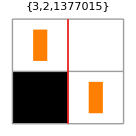

```mathematica
nb=1377015;s=3;k=2;limit=145;{Clear[tm];tm=TuringMachine[WolframInstructionsTable[nb,{s,k}],{{1,0},{{},0}},limit];
step=If[MemberQ[Transpose[Transpose[tm][[1]]][[3]],1],First[Position[Transpose[Transpose[tm][[1]]][[3]],1]][[1]],limit]-1;Clear[tm];tm=TuringMachine[WolframInstructionsTable[nb,{s,k}],{{1,0},{{},0}},step];
delta=If[1-Min[Transpose[Transpose[tm][[1]]][[3]]]>0,1-Min[Transpose[Transpose[tm][[1]]][[3]]],0];
tm12=Transpose[Transpose[tm][[1]]][[2]];tm11=Transpose[Transpose[tm][[1]]][[1]];f[nb]=ArrayPlot[Last/@tm,Mesh->True,PlotLabel->{s,k,nb},LabelStyle->Directive[Bold],Epilog->{{Red,Thick,Line[{{delta,0},{delta,step+1}}]},Orange,Thickness[0.15/(step+1)],Arrowheads[0.5/(step+1)],Table[Rotate[Arrow[{{-1/2+tm12[[i]],2/10+1+step-i},{-1/2+tm12[[i]],4/5+1+step-i}}],-2π/s(tm11[[i]]-1)],{i,step+1}]}]};f[nb]
```

# 5 States

```mathematica
WolframInstructionsTable[nb_,{s_,k_}]:=Thread[Flatten[Table[{i+1,j},{i,s-1,0,-1},{j,k-1,0,-1}],1]->({(#-Mod[#,2]-2Mod[(#-Mod[#,2])/2,k])/(2k)+1,Mod[(#-Mod[#,2])/2,k],2Mod[#,2]-1}&/@PadLeft[IntegerDigits[nb,2s k],s k])]
```

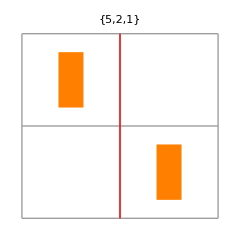

```mathematica
nb=1;s=5;k=2;limit=145;{Clear[tm];tm=TuringMachine[WolframInstructionsTable[nb,{s,k}],{{1,0},{{},0}},limit];
step=If[MemberQ[Transpose[Transpose[tm][[1]]][[3]],1],First[Position[Transpose[Transpose[tm][[1]]][[3]],1]][[1]],limit]-1;Clear[tm];tm=TuringMachine[WolframInstructionsTable[nb,{s,k}],{{1,0},{{},0}},step];
delta=If[1-Min[Transpose[Transpose[tm][[1]]][[3]]]>0,1-Min[Transpose[Transpose[tm][[1]]][[3]]],0];
tm12=Transpose[Transpose[tm][[1]]][[2]];tm11=Transpose[Transpose[tm][[1]]][[1]];f[nb]=ArrayPlot[Last/@tm,Mesh->True,PlotLabel->{s,k,nb},LabelStyle->Directive[Bold],Epilog->{{Red,Thick,Line[{{delta,0},{delta,step+1}}]},Orange,Thickness[0.15/(step+1)],Arrowheads[0.5/(step+1)],Table[Rotate[Arrow[{{-1/2+tm12[[i]],2/10+1+step-i},{-1/2+tm12[[i]],4/5+1+step-i}}],-2π/s(tm11[[i]]-1)],{i,step+1}]}]};f[nb]
```